```mathematica
?AnimatedImage
```

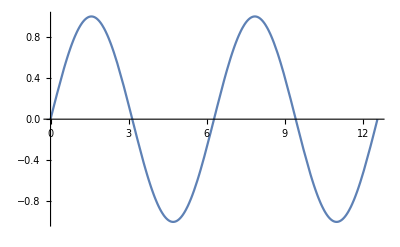

```mathematica
Plot[Sin[t],{t,0,4π}]
```

```mathematica
n=30;
ListAnimate[Table[Plot[Sin[t],{t,0,t′+$MachineEpsilon},PlotRange->{{0,4π},{-1.02,1.02}}],{t′,0,4π,4π/n}]]
```